```mathematica
path=FileNameJoin[{NotebookDirectory[],"times"}];
```

```mathematica
path="/tmp/times";
```

```mathematica
lines=Import[path,"Text"];
```

```mathematica
lines=StringSplit[lines,"\n"];
```

```mathematica
dates=ParallelMap[DateList,lines];
```

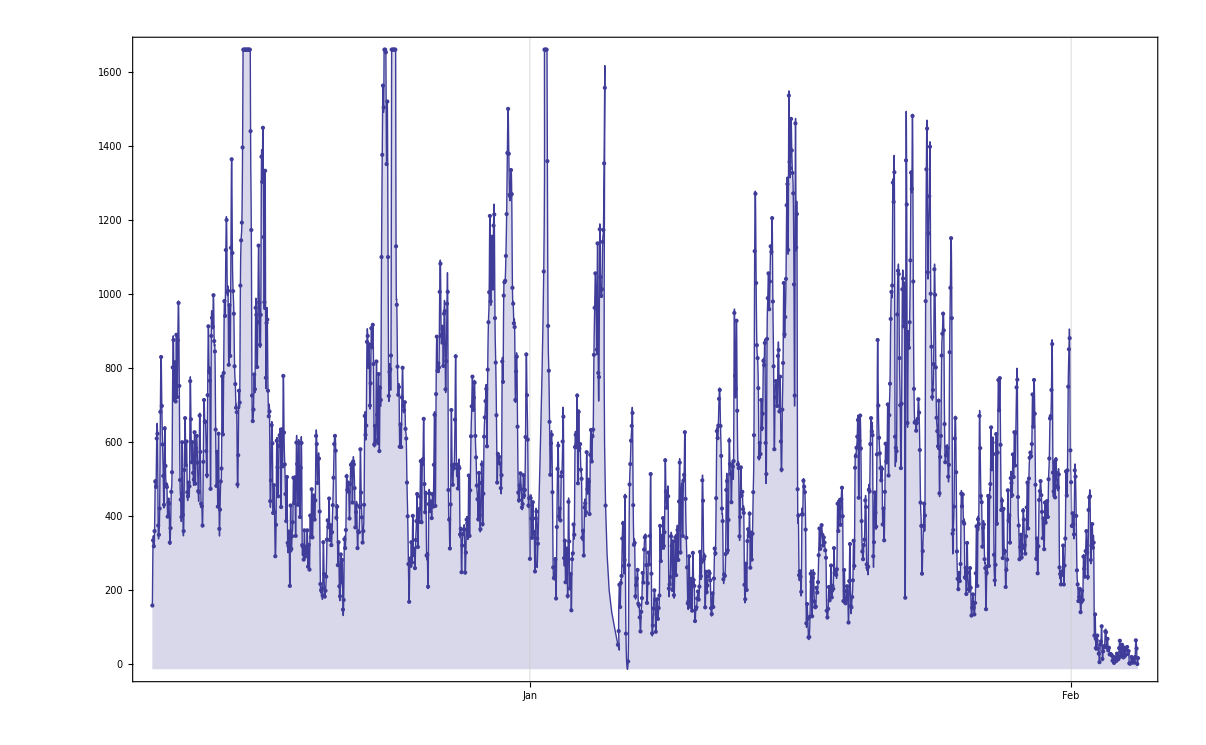

```mathematica
DateListPlot[Sort@Tally[dates[[All,;;-3]]],Joined->True,Mesh->Full,Filling->Bottom,InterpolationOrder->2,LabelStyle->Medium]
```

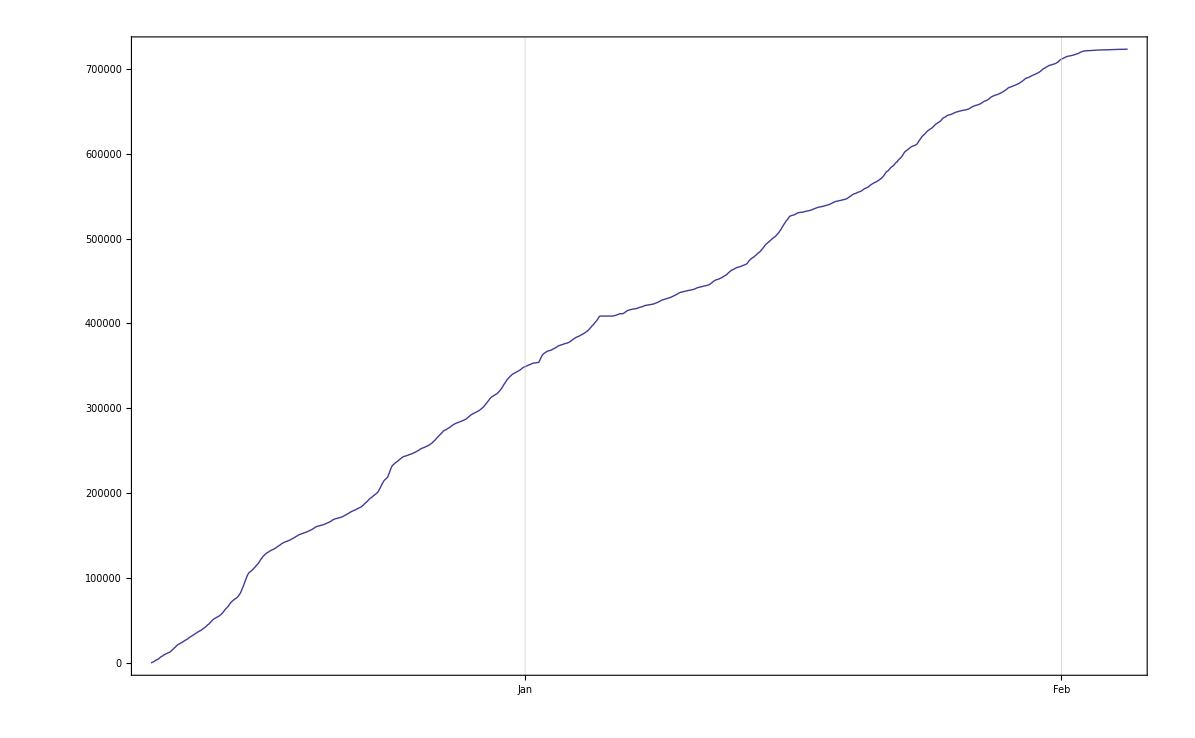

```mathematica
dt=Sort@Tally[dates[[All,;;-3]]];
DateListPlot[Transpose[{Transpose[dt][[1]],Accumulate[Transpose[dt][[2]]]}],Joined->True,LabelStyle->Medium]
```

```mathematica
Length[dates]
```

723143